#### Binarize

Find pixels where the red channel is larger than the green channel :

```mathematica
Binarize[-Graphics-,#[[1]]>#[[2]]+0.15&]
```

-Graphics-

Binarize a gradient image with a specific black fraction to find the strongest edges :

```mathematica
{Binarize[GradientFilter[-Graphics-,1],Method->{"BlackFraction",.8}],EdgeDetect[-Graphics-]}
```

{-Graphics-,-Graphics-}

create a mask by using the alpha channel.

```mathematica
image=-Graphics-;
alpha=Binarize[image,2/3]
SetAlphaChannel[image,DeleteSmallComponents[alpha]]
```

-Graphics-

-Graphics-

ChanVeseBinarize finds optimal contours around regions of consistent color:

```mathematica
{Binarize[image,2/3],ChanVeseBinarize[image,Yellow]}
```

{-Graphics-,-Graphics-}

#### ChanVeseBinarize

Specify the foreground color to be used for an initial marker:

```mathematica
Through[{ChanVeseBinarize[#,Red]&,ChanVeseBinarize,Binarize}[-Graphics-]]
```

{-Graphics-,-Graphics-,-Graphics-}

Specify both foreground and background colors for creating an initial marker:

```mathematica
ChanVeseBinarize[-Graphics-,{{Red,Blue}}]
```

-Graphics-

Use foreground edges as the marker image:

```mathematica
i = -Graphics-;
Through[{Binarize,ChanVeseBinarize,ChanVeseBinarize[#,{{Green,Blue}}]&}[i]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ChanVeseBinarize[i,EdgeDetect[i]]
```

-Graphics-

Image Composing

```mathematica
RGBColor[0,.7,.4]
```

RGBColor[0, 0.7, 0.4]

```mathematica
i=-Graphics-;
ColorNegate@ChanVeseBinarize[i,RGBColor[0,.7,.4],{1},MaxIterations->1]
ii=SetAlphaChannel[i,%]
ImageCompose[-Graphics-,ii]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ImageDimensions/@{ii,-Graphics-}
```

{{250,200},{250,200}}

Improve text recognition

```mathematica
image=-Graphics-;
TextRecognize[image]
```

1 \_=# ggi :_  >i»  9,
@.,~.~ ~   » we
V
  W' ;l,d~z;
 
ww ;f;n»>=;_A,

```mathematica
Through[{Binarize,ChanVeseBinarize,ChanVeseBinarize[#,{{Black,Yellow}}]&,ChanVeseBinarize[#,{{Black,Yellow}},{0.55}]&}[image]]
TextRecognize/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{~/wi ig
  `,__ A    
      ff
 
av <   ‘.é‘~'~1“,.EJ . :»
     
-;»~:@>;,§w@#@=ffq&¢¢mv
,wg  w»;¢»»»4-,~. my ~»»=
§L;,<5`~;$;~¥»:< "V '5;’rc_
E 5 i?¢m1;e~h:r ”   ww.,  
;;;»¢’f,é<w  
 
s"-c ~ =, ' A, _ .~ TTL.
;¢;¢2@§, :ay @2~z‘l;?¢$:f~z<:
 
,N   __ ,._.,
  ` M
  Q.; , ,aé
{%?»Hxl>`5°w'if£ WL ,'f»'2fivR"rf,w‘f,»9“*1'f?3‘f;
 . ’*¥9f§‘S¥*
` \ »
if§f£ffS?f  
Pf#§'ff§h,One fish
two fish
red fish
blue fish}

#### FillingTransform

Remove background features from an astronomical image:

```mathematica
img = -Graphics-;
bkground=ColorNegate@FillingTransform[ColorNegate[img]]
ImageSubtract[img,bkground]
```

-Graphics-

-Graphics-

#### MorphologicalComponents

```mathematica
MorphologicalComponents[-Graphics-]//ArrayPlot
```

-Graphics-

Count the number of bright spots, specifying an explicit thresholding value:

```mathematica
MorphologicalComponents[-Graphics-,0.8]//ArrayPlot
MorphologicalComponents[-Graphics-,0.8]//Max
MorphologicalComponents[-Graphics-,0.8]//Flatten//Tally
```

-Graphics-

3

{{0,22415},{1,14},{2,35},{3,36}}

Find connected regions in a map

```mathematica
MorphologicalComponents[-Graphics-] //Colorize
```

-Graphics-

#### SelectComponents

```mathematica
i=-Graphics-;
ComponentMeasurements[-Graphics-,"EmbeddedComponents"]
m=SelectComponents[i,"EmbeddedComponents",Length[#]===0&]
SelectComponents[i,"EmbeddedComponents",Length[#]===1&]
SelectComponents[i,"EmbeddedComponents",Length[#]===2&]
```

{1→{2,3},2→{3},3→{},4→{6,8},5→{7,9},6→{8},7→{9},8→{},9→{}}

-Graphics-

-Graphics-

-Graphics-

```mathematica
FillingTransform[i,Dilation[m,.5]]
```

-Graphics-

{1→{2,3},2→{3},3→{},4→{6,8},5→{7,9},6→{8},7→{9},8→{},9→{}}

Remove disks larger than the structuring element:

```mathematica
TopHatTransform[-Graphics-,DiskMatrix[7]]
```

-Graphics-

Correct uneven illumination and remove the large feature:

```mathematica
TopHatTransform[-Graphics-,2]
```

-Graphics-

Subtract the top-hat transform of an image to remove small features:

```mathematica
ImageSubtract[#, TopHatTransform[#,4]]&[-Graphics-]
```

-Graphics-

Correct uneven background illumination in a grayscale image:

```mathematica
TopHatTransform[-Graphics-,4]
```

-Graphics-

Isolate the lightning from an image:

```mathematica
TopHatTransform[-Graphics-,3]
```

-Graphics-

The bottom-hat transform effectively inverts high-frequency regions:

```mathematica
BottomHatTransform[-Graphics-,7]
```

-Graphics-

find salt-and-pepper noise

```mathematica
img=-Graphics-;
Through[{MaxDetect,MinDetect}[img]]
ImageAdd@@%
Inpaint[img,%]
```

{-Graphics-,-Graphics-}

-Graphics-

-Graphics-

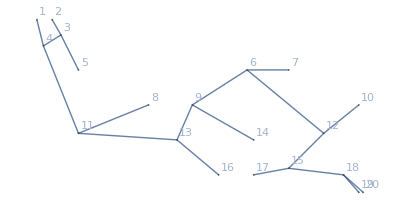

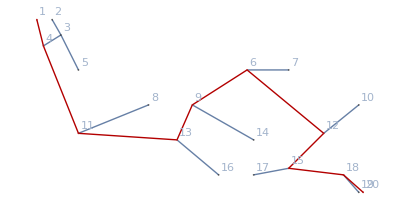

```mathematica
g=MorphologicalGraph[-Graphics-,VertexLabels-> "Name"]
HighlightGraph[g,PathGraph[FindShortestPath[g,1,20]]]
```

Morphological thinning of an image:

```mathematica
Thinning[-Graphics-]
```

-Graphics-

Simplify features in a fingerprint image:

```mathematica
Thinning[-Graphics-]
```

-Graphics-

Extract possible paths through a maze:

```mathematica
Pruning[Thinning[-Graphics-,Padding->1],Padding->1]
```

-Graphics-

```mathematica
Pruning[Thinning[-Graphics-],Infinity]
```

-Graphics-